```mathematica
(* Circle-circle intersection *)
ℛ1=Circle[{x1,y1}, r1]/.{x1-> 1,y1-> 2, r1->3};
ℛ2=Circle[{x2,y2}, r2]/.{x2-> -1,y2-> 3, r2->2};
```

```mathematica
pts=Solve[{x,y}∈ℛ1&&{x,y}∈ℛ2,{x, y}]
```

{{x→1/5 (-5-2 √5),y→5+2/5 (-5-2 √5)},{x→1/5 (-5+2 √5),y→5+2/5 (-5+2 √5)}}

```mathematica
ℒ1=Line[{{x,y}/.pts⟦1⟧,{x,y}/.pts⟦2⟧}]
```

Line[{{1/5 (-5-2 √5),5+2/5 (-5-2 √5)},{1/5 (-5+2 √5),5+2/5 (-5+2 √5)}}]

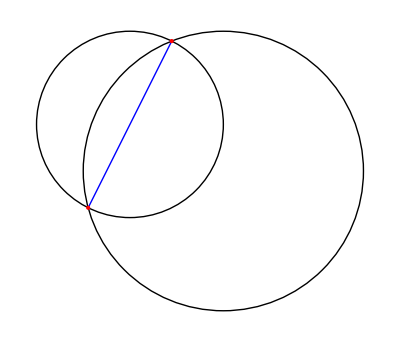

```mathematica
Graphics[{ℛ1,ℛ2,{Blue,ℒ1},{Red,PointSize[Medium],Point[{x,y}/.pts]}}]
```